## Bounds on EDGB Theory From the Overall Posterior of GW150914

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"];(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-phase-only-beta.csv","CSV"] (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-amp-only-alpha.csv","CSV"]; (*PPE alpha*)
```

{{0.0000835696},{0.0000857924},{0.000088643},{0.0000848591},{0.000083665},{0.0000983828},{0.000086322},16319,{0.000088384},{0.0000877578},{0.0000874088},{0.0000947909},{0.000093868},{0.0000892042}}
 |  |  |  |

```mathematica
0.000085792380799407//ScientificForm
```

8.57924×10^-5

```mathematica
5.72*10^-4*3*10^5
```

171.6

```mathematica
dataOverall4=Import[NotebookDirectory[]<>"/-1pn-combined-correlated-beta.csv","CSV"]; (*PPE beta for phase and amp combined*)
```

```mathematica
χ1All=dataOverall1[[All,7]]
 (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]]
```

{0.394141,0.70691,0.0187798,0.114828,0.403775,0.14829,0.0677458,0.191806,16316,0.218852,0.577305,0.0555225,0.00655742,0.19115,0.927746,0.0369487,0.11068}
 |  |  |  |

{0.0330915,0.434739,0.29455,0.130313,0.335006,0.0465671,0.396861,0.3978,16316,0.983343,0.266759,0.0128517,0.0196094,0.0124044,0.558997,0.307429,0.423524}
 |  |  |  |

```mathematica
DL=dataOverall1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,16318,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,16317,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
m1All=dataOverall1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 (*Ligo posterior gives mass in detector frame*)
m2All=dataOverall1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.000164382,0.000172434,0.000186598,0.000166746,0.000160002,0.000214392,16320,0.000185522,0.000178181,0.000180393,0.000202519,0.000202124,0.000185951}
 |  |  |  |

{0.000154056,0.000150252,0.00013417,0.000166077,0.000153064,0.000129181,0.000164308,16318,0.000135998,0.000145104,0.000141122,0.000145081,0.000126583,0.000133266,0.000149862}
 |  |  |  |

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=dataOverall2[[All,1]](*1-sigma upper bound*)
αppEAll=dataOverall3[[All,1]](*1-sigma upper bound*)
```

{0.0000835696,0.0000857924,0.000088643,0.0000848591,0.000083665,0.0000983828,0.000086322,16318,0.0000879308,0.000088384,0.0000877578,0.0000874088,0.0000947909,0.000093868,0.0000892042}
 |  |  |  |

{0.0161963,0.0168031,0.0158669,0.0167165,0.0161385,0.0154321,0.0171932,0.0157346,16316,0.0162675,0.0158457,0.0161739,0.0160464,0.0161101,0.0159761,0.015686,0.0166971}
 |  |  |  |

```mathematica
βppEComb=dataOverall4[[All,1]]
```

{0.0000904525,0.0000931781,0.0000958978,0.0000920836,0.0000906122,0.000105868,0.0000937855,16318,0.0000950742,0.00009579,0.0000949968,0.0000945403,0.000102339,0.000101574,0.0000968086}
 |  |  |  |

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2)
```

{0.999726,0.947677,0.977315,0.995718,0.970248,0.999457,0.957181,0.95696,16316,0.30761,0.981547,0.999959,0.999904,0.999962,0.906608,0.975185,0.950619}
 |  |  |  |

```mathematica
factor=(7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2))^-1*16*π/(m1All+m2All)^4 (*factor to match with Fisher code*)
```

{8.97427×10^11,4.00241×10^12,1.30283×10^13,1.30269×10^9,3.36572×10^11,2.87335×10^13,2.38272×10^11,16318,1.33235×10^13,6.82157×10^12,7.01197×10^12,5.836×10^12,3.69867×10^13,1.83414×10^13,3.65127×10^12}
 |  |  |  |

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] (*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*)
```

{0.455216,0.0993743,0.0323046,266.856,1.30075,0.0123516,1.34769,0.0678463,16316,0.225596,0.032577,0.0545013,0.0605206,0.0670878,0.0109816,0.0203308,0.0965651}
 |  |  |  |

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll](*Sigma_Zeta from amplitude corrections*)
```

{2.36314,0.521335,0.154888,1408.08,6.72076,0.0518959,7.19001,0.328494,16316,1.08675,0.157248,0.267148,0.296414,0.331201,0.0495765,0.0910027,0.484149}
 |  |  |  |

```mathematica
ζcombAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEComb]
```

{0.492707,0.107929,0.0349485,289.575,1.40876,0.0132914,1.46422,0.0733173,16317,0.0352235,0.0590682,0.0655128,0.0725613,0.0118561,0.0219998,0.104797}
 |  |  |  |

```mathematica
Length[m1All]
```

16332

```mathematica
Length[βppEAll]
```

16332

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

12664

```mathematica
Length[ζAllampSelected]
```

8537

```mathematica
Mean[ζAllphaseSelected]
```

0.197183

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.217444

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.455216},{1},16329,{-0.960167,432.955,7,0.304489,0.0965651}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.455216,2.36314},16330,{-0.960167,432.955,8,0.0965651,0.484149}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] ;(*Data satisfying zeta_phase<1*)
```

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{-0.835255,614.169,2.3996,-1.15619,39.5694,34.4793,0.70691,0.434739,-0.100755,0.415459,0.0993743,0.521335},8535,{-0.960167,432.955,8,0.0965651,0.484149}}
 |  |  |  |

```mathematica
A4[[All,12]];
```

```mathematica
Length[A3]
```

12664

```mathematica
Length[A4]
```

8537

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.38243

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5;(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{29.4702,20.4128,15.3218,151.56,37.6693,12.9049,41.3888,17.9502,16316,26.1325,15.2055,17.9988,17.8436,18.663,12.0033,14.269,21.0915}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBphase]
```

33.5942

```mathematica
StandardDeviation[SqrtαEDGBphase]
```

48.9756

```mathematica
SqrtαEDGBcomb=((ζcombAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{30.0591,20.8386,15.6261,154.688,38.4281,13.1436,42.2559,18.3016,16316,26.6656,15.5054,18.3645,18.2007,19.0325,12.2355,14.5532,21.5273}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

50.612

```mathematica
Mean[SqrtαEDGBphase]
```

33.5942

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{13.5335,12.0647,10.9171,20.0839,14.5154,10.2304,14.892,11.5504,16316,13.0527,10.8866,11.5612,11.5266,11.7062,9.94074,10.6323,12.1955}
 |  |  |  |

```mathematica
MaxLogSquaredαPhase=Max[LogSquaredαPhase]
```

31.8781

```mathematica
MinLogSquaredαPhase=Min[LogSquaredαPhase]
```

9.03324

```mathematica
(*𝒟logα=HistogramDistribution[LogSquaredαPhase] ;*)
```

```mathematica
(*pslogαPhase=PDF[𝒟logα,x];*)
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
(*fun1αphase[x_,y_]=1/(√(2*π)*Exp[y]/1.64485)*Exp[-x^2/(2*Exp[2*y]/1.64485^2)] *)
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2*Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-7,15,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}];(*Table for fun1αphase*)
```

```mathematica
(*αPhaseMC[x_]=pslogαPhase*)
```

```mathematica
(*αPhaseMC[5]*)
```

```mathematica
(*αPhaseMC[33]*)
```

```mathematica
(*αMCSample=Range[5,37,1.1];*)
```

```mathematica
(*αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];*)
```

```mathematica
(*αMCTableInterp=Interpolation[αMCTable];*)
```

```mathematica
(*plotαMCTableInterp=Plot[αMCTableInterp[x],{x,5,37},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]*)
```

```mathematica
(*plot5=Plot[αPhaseMC[x],{x,5,37},Filling->Axis,PlotStyle->Gray,PlotRange->All]*)
```

```mathematica
(*Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)*)
```

```mathematica
𝒟logαSq=SmoothKernelDistribution[LogSquaredαPhase]
```

DataDistribution[…]

```mathematica
𝒟logαSq2=PDF[𝒟logαSq,x]
```

Piecewise[{{InterpolatingFunction[…][x], 7.79758≤x≤33.1137}, {0, True}}]

```mathematica
𝒟logαSq3[x_]=𝒟logαSq2
```

Piecewise[{{InterpolatingFunction[…][x], 7.79758≤x≤33.1137}, {0, True}}]

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]𝒟logαSq3[y],{y,MinLogSquaredαPhase,MaxLogSquaredαPhase}]},{i,1,Length[fun1αphaseTable[y]]}]
```

{{0,2.81088×10^-6},{1.×10^-7,2.81088×10^-6},{1.25893×10^-7,2.81088×10^-6},{1.58489×10^-7,2.81088×10^-6},{1.99526×10^-7,2.81088×10^-6},{2.51189×10^-7,2.81088×10^-6},{3.16228×10^-7,2.81088×10^-6},{3.98107×10^-7,2.81088×10^-6},{5.01187×10^-7,2.81088×10^-6},{6.30957×10^-7,2.81088×10^-6},{7.94328×10^-7,2.81088×10^-6},{1.×10^-6,2.81088×10^-6},{1.25893×10^-6,2.81088×10^-6},{1.58489×10^-6,2.81088×10^-6},{1.99526×10^-6,2.81088×10^-6},{2.51189×10^-6,2.81088×10^-6},{3.16228×10^-6,2.81088×10^-6},{3.98107×10^-6,2.81088×10^-6},{5.01187×10^-6,2.81088×10^-6},{6.30957×10^-6,2.81088×10^-6},{7.94328×10^-6,2.81088×10^-6},{0.00001,2.81088×10^-6},{0.0000125893,2.81088×10^-6},{0.0000158489,2.81088×10^-6},{0.0000199526,2.81088×10^-6},{0.0000251189,2.81088×10^-6},{0.0000316228,2.81088×10^-6},{0.0000398107,2.81088×10^-6},{0.0000501187,2.81088×10^-6},{0.0000630957,2.81088×10^-6},{0.0000794328,2.81088×10^-6},{0.0001,2.81088×10^-6},{0.000125893,2.81088×10^-6},{0.000158489,2.81088×10^-6},{0.000199526,2.81088×10^-6},{0.000251189,2.81088×10^-6},{0.000316228,2.81088×10^-6},{0.000398107,2.81088×10^-6},{0.000501187,2.81088×10^-6},{0.000630957,2.81088×10^-6},{0.000794328,2.81088×10^-6},{0.001,2.81088×10^-6},{0.00125893,2.81088×10^-6},{0.00158489,2.81088×10^-6},{0.00199526,2.81088×10^-6},{0.00251189,2.81088×10^-6},{0.00316228,2.81088×10^-6},{0.00398107,2.81088×10^-6},{0.00501187,2.81088×10^-6},{0.00630957,2.81088×10^-6},{0.00794328,2.81088×10^-6},{0.01,2.81088×10^-6},{0.0125893,2.81088×10^-6},{0.0158489,2.81088×10^-6},{0.0199526,2.81088×10^-6},{0.0251189,2.81088×10^-6},{0.0316228,2.81088×10^-6},{0.0398107,2.81088×10^-6},{0.0501187,2.81088×10^-6},{0.0630957,2.81088×10^-6},{0.0794328,2.81088×10^-6},{0.1,2.81088×10^-6},{0.125893,2.81088×10^-6},{0.158489,2.81088×10^-6},{0.199526,2.81088×10^-6},{0.251189,2.81088×10^-6},{0.316228,2.81088×10^-6},{0.398107,2.81088×10^-6},{0.501187,2.81088×10^-6},{0.630957,2.81088×10^-6},{0.794328,2.81088×10^-6},{1.,2.81088×10^-6},{1.25893,2.81088×10^-6},{1.58489,2.81088×10^-6},{1.99526,2.81088×10^-6},{2.51189,2.81088×10^-6},{3.16228,2.81088×10^-6},{3.98107,2.81088×10^-6},{5.01187,2.81088×10^-6},{6.30957,2.81088×10^-6},{7.94328,2.81088×10^-6},{10.,2.81088×10^-6},{12.5893,2.81088×10^-6},{15.8489,2.81088×10^-6},{19.9526,2.81088×10^-6},{25.1189,2.81088×10^-6},{31.6228,2.81088×10^-6},{39.8107,2.81088×10^-6},{50.1187,2.81087×10^-6},{63.0957,2.81087×10^-6},{79.4328,2.81087×10^-6},{100.,2.81087×10^-6},{125.893,2.81086×10^-6},{158.489,2.81085×10^-6},{199.526,2.81083×10^-6},{251.189,2.8108×10^-6},{316.228,2.81076×10^-6},{398.107,2.81069×10^-6},{501.187,2.81057×10^-6},{630.957,2.81039×10^-6},{794.328,2.81011×10^-6},{1000.,2.80966×10^-6},{1258.93,2.80895×10^-6},{1584.89,2.80783×10^-6},{1995.26,2.80605×10^-6},{2511.89,2.80325×10^-6},{3162.28,2.79882×10^-6},{3981.07,2.79187×10^-6},{5011.87,2.781×10^-6},{6309.57,2.76414×10^-6},{7943.28,2.73829×10^-6},{10000.,2.69931×10^-6},{12589.3,2.64199×10^-6},{15848.9,2.56051×10^-6},{19952.6,2.44952×10^-6},{25118.9,2.3056×10^-6},{31622.8,2.12856×10^-6},{39810.7,1.92231×10^-6},{50118.7,1.69517×10^-6},{63095.7,1.45881×10^-6},{79432.8,1.22576×10^-6},{100000.,1.0067×10^-6},{125893.,8.09062×10^-7},{158489.,6.36959×10^-7},{199526.,4.91875×10^-7},{251189.,3.7326×10^-7},{316228.,2.79041×10^-7},{398107.,2.06138×10^-7},{501187.,1.50958×10^-7},{630957.,1.09861×10^-7},{794328.,7.95647×10^-8},{1.×10^6,5.73852×10^-8},{1.25893×10^6,4.1253×10^-8},{1.58489×10^6,2.95995×10^-8},{1.99526×10^6,2.12266×10^-8},{2.51189×10^6,1.52239×10^-8},{3.16228×10^6,1.09191×10^-8},{3.98107×10^6,7.82915×10^-9},{5.01187×10^6,5.60793×10^-9},{6.30957×10^6,4.00757×10^-9},{7.94328×10^6,2.853×10^-9},{1.×10^7,2.02272×10^-9},{1.25893×10^7,1.43091×10^-9},{1.58489×10^7,1.01319×10^-9},{1.99526×10^7,7.19528×10^-10},{2.51189×10^7,5.1238×10^-10},{3.16228×10^7,3.65329×10^-10},{3.98107×10^7,2.60366×10^-10},{5.01187×10^7,1.85142×10^-10},{6.30957×10^7,1.31168×10^-10},{7.94328×10^7,9.25808×10^-11},{1.×10^8,6.51534×10^-11},{1.25893×10^8,4.57211×10^-11},{1.58489×10^8,3.19755×10^-11},{1.99526×10^8,2.22931×10^-11},{2.51189×10^8,1.55181×10^-11},{3.16228×10^8,1.08085×10^-11},{3.98107×10^8,7.55254×10^-12},{5.01187×10^8,5.30591×10^-12},{6.30957×10^8,3.74645×10^-12},{7.94328×10^8,2.64739×10^-12},{1.×10^9,1.86006×10^-12},{1.25893×10^9,1.29428×10^-12},{1.58489×10^9,8.94279×10^-13},{1.99526×10^9,6.18627×10^-13},{2.51189×10^9,4.3241×10^-13},{3.16228×10^9,3.07507×10^-13},{3.98107×10^9,2.23101×10^-13},{5.01187×10^9,1.64815×10^-13},{6.30957×10^9,1.23212×10^-13},{7.94328×10^9,9.22973×10^-14},{1.×10^10,6.85792×10^-14},{1.25893×10^10,5.02668×10^-14},{1.58489×10^10,3.63135×10^-14},{1.99526×10^10,2.58349×10^-14},{2.51189×10^10,1.80353×10^-14},{3.16228×10^10,1.22956×10^-14},{3.98107×10^10,8.20033×10^-15},{5.01187×10^10,5.44811×10^-15},{6.30957×10^10,3.71975×10^-15},{7.94328×10^10,2.66104×10^-15},{1.×10^11,1.97741×10^-15},{1.25893×10^11,1.49481×10^-15},{1.58489×10^11,1.1344×10^-15},{1.99526×10^11,8.59538×10^-16},{2.51189×10^11,6.46245×10^-16},{3.16228×10^11,4.7802×10^-16},{3.98107×10^11,3.45578×10^-16},{5.01187×10^11,2.43721×10^-16},{6.30957×10^11,1.68091×10^-16},{7.94328×10^11,1.13834×10^-16},{1.×10^12,7.57423×10^-17},{1.25893×10^12,4.91612×10^-17},{1.58489×10^12,3.0769×10^-17},{1.99526×10^12,1.85327×10^-17},{2.51189×10^12,1.09757×10^-17},{3.16228×10^12,6.61758×10^-18},{3.98107×10^12,4.11003×10^-18},{5.01187×10^12,2.60662×10^-18},{6.30957×10^12,1.74258×10^-18},{7.94328×10^12,1.32377×10^-18},{1.×10^13,1.15357×10^-18},{1.25893×10^13,1.06985×10^-18},{1.58489×10^13,9.89434×10^-19},{1.99526×10^13,8.84304×10^-19},{2.51189×10^13,7.48994×10^-19},{3.16228×10^13,5.90109×10^-19},{3.98107×10^13,4.2572×10^-19},{5.01187×10^13,2.79967×10^-19},{6.30957×10^13,1.70059×10^-19},{7.94328×10^13,9.67507×10^-20},{1.×10^14,4.98626×10^-20},{1.25893×10^14,2.08886×10^-20},{1.58489×10^14,6.02341×10^-21},{1.99526×10^14,9.56545×10^-22},{2.51189×10^14,6.05037×10^-23},{3.16228×10^14,9.20001×10^-25},{3.98107×10^14,1.50436×10^-27},{5.01187×10^14,7.32923×10^-32},{6.30957×10^14,1.38052×10^-38},{7.94328×10^14,3.9291×10^-49},{1.×10^15,9.88099×10^-66}}

```mathematica
(*Export[NotebookDirectory[]<>"cdf.dat",αFinalPDFPhaseLog]*)
```

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog]
```

InterpolatingFunction[…]

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,10^15}]
```

0.499356

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

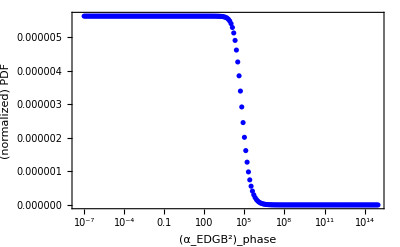

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLinearPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

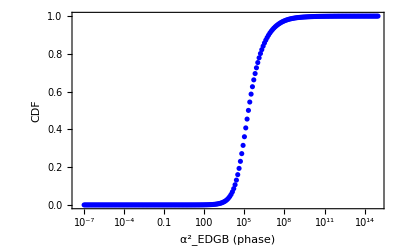

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

6.48077×10^6

```mathematica
√√αSquared90CLphase//N   (*90% CL upper bound*)
```

50.4553

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{15.1805,13.7222,12.4846,21.7472,16.1576,11.6659,16.5663,13.1277,16316,14.6249,12.4609,13.1508,13.1154,13.3029,11.448,12.1311,13.8076}
 |  |  |  |

```mathematica
MaxLogSquaredαamp=Max[LogSquaredαamp]
```

33.5467

```mathematica
MinLogSquaredαamp=Min[LogSquaredαamp]
```

10.565

```mathematica
𝒟logαamp=SmoothKernelDistribution[LogSquaredαamp]
```

DataDistribution[…]

```mathematica
𝒟logαamp2=PDF[𝒟logαamp,x]
```

Piecewise[{{InterpolatingFunction[…][x], 9.30588≤x≤34.8058}, {0, True}}]

```mathematica
𝒟logαamp3[x_]=𝒟logαamp2
```

Piecewise[{{InterpolatingFunction[…][x], 9.30588≤x≤34.8058}, {0, True}}]

```mathematica
(*𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;*)
```

```mathematica
(*pslogαamp=PDF[𝒟logαamp,x];*)
```

```mathematica
(*Histogram[LogSquaredαamp];*)
```

```mathematica
(*αampMC[x_]=pslogαamp;*)
```

```mathematica
(*αampMC[35]*)
```

```mathematica
(*αampMC[5]*)
```

```mathematica
(*αMCSampleamp=Range[5,35,1.2];*)
```

```mathematica
(*αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];*)
```

```mathematica
(*αMCTableInterpamp=Interpolation[αMCTableamp];*)
```

```mathematica
(*plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,9,34},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]*)
```

```mathematica
(*plot6=Plot[αampMC[x],{x,9,34},Filling->Axis,PlotStyle->Gray,PlotRange->All]*)
```

```mathematica
(*Show[plot6,plotαMCTableInterpamp]*)
```

```mathematica
αSampleLogamp=Prepend[10^Range[-7,15.5,0.1],0]
```

{0,1.×10^-7,1.25893×10^-7,1.58489×10^-7,1.99526×10^-7,2.51189×10^-7,3.16228×10^-7,3.98107×10^-7,5.01187×10^-7,6.30957×10^-7,7.94328×10^-7,1.×10^-6,1.25893×10^-6,1.58489×10^-6,1.99526×10^-6,2.51189×10^-6,3.16228×10^-6,3.98107×10^-6,5.01187×10^-6,6.30957×10^-6,7.94328×10^-6,0.00001,0.0000125893,0.0000158489,0.0000199526,0.0000251189,0.0000316228,0.0000398107,0.0000501187,0.0000630957,0.0000794328,0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6,25118.9,31622.8,39810.7,50118.7,63095.7,79432.8,100000.,125893.,158489.,199526.,251189.,316228.,398107.,501187.,630957.,794328.,1.×10^6,1.25893×10^6,1.58489×10^6,1.99526×10^6,2.51189×10^6,3.16228×10^6,3.98107×10^6,5.01187×10^6,6.30957×10^6,7.94328×10^6,1.×10^7,1.25893×10^7,1.58489×10^7,1.99526×10^7,2.51189×10^7,3.16228×10^7,3.98107×10^7,5.01187×10^7,6.30957×10^7,7.94328×10^7,1.×10^8,1.25893×10^8,1.58489×10^8,1.99526×10^8,2.51189×10^8,3.16228×10^8,3.98107×10^8,5.01187×10^8,6.30957×10^8,7.94328×10^8,1.×10^9,1.25893×10^9,1.58489×10^9,1.99526×10^9,2.51189×10^9,3.16228×10^9,3.98107×10^9,5.01187×10^9,6.30957×10^9,7.94328×10^9,1.×10^10,1.25893×10^10,1.58489×10^10,1.99526×10^10,2.51189×10^10,3.16228×10^10,3.98107×10^10,5.01187×10^10,6.30957×10^10,7.94328×10^10,1.×10^11,1.25893×10^11,1.58489×10^11,1.99526×10^11,2.51189×10^11,3.16228×10^11,3.98107×10^11,5.01187×10^11,6.30957×10^11,7.94328×10^11,1.×10^12,1.25893×10^12,1.58489×10^12,1.99526×10^12,2.51189×10^12,3.16228×10^12,3.98107×10^12,5.01187×10^12,6.30957×10^12,7.94328×10^12,1.×10^13,1.25893×10^13,1.58489×10^13,1.99526×10^13,2.51189×10^13,3.16228×10^13,3.98107×10^13,5.01187×10^13,6.30957×10^13,7.94328×10^13,1.×10^14,1.25893×10^14,1.58489×10^14,1.99526×10^14,2.51189×10^14,3.16228×10^14,3.98107×10^14,5.01187×10^14,6.30957×10^14,7.94328×10^14,1.×10^15,1.25893×10^15,1.58489×10^15,1.99526×10^15,2.51189×10^15,3.16228×10^15}

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]*𝒟logαamp3[y],{y,MinLogSquaredαamp,MaxLogSquaredαPhase}]},{i,1,Length[fun1αampTable[y]]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0,5.88105×10^-7},{1.×10^-7,5.88105×10^-7},{1.25893×10^-7,5.88105×10^-7},{1.58489×10^-7,5.88105×10^-7},{1.99526×10^-7,5.88105×10^-7},{2.51189×10^-7,5.88105×10^-7},{3.16228×10^-7,5.88105×10^-7},{3.98107×10^-7,5.88105×10^-7},{5.01187×10^-7,5.88105×10^-7},{6.30957×10^-7,5.88105×10^-7},{7.94328×10^-7,5.88105×10^-7},{1.×10^-6,5.88105×10^-7},{1.25893×10^-6,5.88105×10^-7},{1.58489×10^-6,5.88105×10^-7},{1.99526×10^-6,5.88105×10^-7},{2.51189×10^-6,5.88105×10^-7},{3.16228×10^-6,5.88105×10^-7},{3.98107×10^-6,5.88105×10^-7},{5.01187×10^-6,5.88105×10^-7},{6.30957×10^-6,5.88105×10^-7},{7.94328×10^-6,5.88105×10^-7},{0.00001,5.88105×10^-7},{0.0000125893,5.88105×10^-7},{0.0000158489,5.88105×10^-7},{0.0000199526,5.88105×10^-7},{0.0000251189,5.88105×10^-7},{0.0000316228,5.88105×10^-7},{0.0000398107,5.88105×10^-7},{0.0000501187,5.88105×10^-7},{0.0000630957,5.88105×10^-7},{0.0000794328,5.88105×10^-7},{0.0001,5.88105×10^-7},{0.000125893,5.88105×10^-7},{0.000158489,5.88105×10^-7},{0.000199526,5.88105×10^-7},{0.000251189,5.88105×10^-7},{0.000316228,5.88105×10^-7},{0.000398107,5.88105×10^-7},{0.000501187,5.88105×10^-7},{0.000630957,5.88105×10^-7},{0.000794328,5.88105×10^-7},{0.001,5.88105×10^-7},{0.00125893,5.88105×10^-7},{0.00158489,5.88105×10^-7},{0.00199526,5.88105×10^-7},{0.00251189,5.88105×10^-7},{0.00316228,5.88105×10^-7},{0.00398107,5.88105×10^-7},{0.00501187,5.88105×10^-7},{0.00630957,5.88105×10^-7},{0.00794328,5.88105×10^-7},{0.01,5.88105×10^-7},{0.0125893,5.88105×10^-7},{0.0158489,5.88105×10^-7},{0.0199526,5.88105×10^-7},{0.0251189,5.88105×10^-7},{0.0316228,5.88105×10^-7},{0.0398107,5.88105×10^-7},{0.0501187,5.88105×10^-7},{0.0630957,5.88105×10^-7},{0.0794328,5.88105×10^-7},{0.1,5.88105×10^-7},{0.125893,5.88105×10^-7},{0.158489,5.88105×10^-7},{0.199526,5.88105×10^-7},{0.251189,5.88105×10^-7},{0.316228,5.88105×10^-7},{0.398107,5.88105×10^-7},{0.501187,5.88105×10^-7},{0.630957,5.88105×10^-7},{0.794328,5.88105×10^-7},{1.,5.88105×10^-7},{1.25893,5.88105×10^-7},{1.58489,5.88105×10^-7},{1.99526,5.88105×10^-7},{2.51189,5.88105×10^-7},{3.16228,5.88105×10^-7},{3.98107,5.88105×10^-7},{5.01187,5.88105×10^-7},{6.30957,5.88105×10^-7},{7.94328,5.88105×10^-7},{10.,5.88105×10^-7},{12.5893,5.88105×10^-7},{15.8489,5.88105×10^-7},{19.9526,5.88105×10^-7},{25.1189,5.88105×10^-7},{31.6228,5.88105×10^-7},{39.8107,5.88105×10^-7},{50.1187,5.88105×10^-7},{63.0957,5.88105×10^-7},{79.4328,5.88105×10^-7},{100.,5.88105×10^-7},{125.893,5.88105×10^-7},{158.489,5.88105×10^-7},{199.526,5.88105×10^-7},{251.189,5.88105×10^-7},{316.228,5.88104×10^-7},{398.107,5.88103×10^-7},{501.187,5.88102×10^-7},{630.957,5.881×10^-7},{794.328,5.88097×10^-7},{1000.,5.88092×10^-7},{1258.93,5.88084×10^-7},{1584.89,5.88072×10^-7},{1995.26,5.88053×10^-7},{2511.89,5.88022×10^-7},{3162.28,5.87973×10^-7},{3981.07,5.87895×10^-7},{5011.87,5.87772×10^-7},{6309.57,5.87577×10^-7},{7943.28,5.87269×10^-7},{10000.,5.86782×10^-7},{12589.3,5.86015×10^-7},{15848.9,5.84806×10^-7},{19952.6,5.82913×10^-7},{25118.9,5.79964×10^-7},{31622.8,5.75419×10^-7},{39810.7,5.68516×10^-7},{50118.7,5.58259×10^-7},{63095.7,5.43483×10^-7},{79432.8,5.23047×10^-7},{100000.,4.96144×10^-7},{125893.,4.62579×10^-7},{158489.,4.22905×10^-7},{199526.,3.78466×10^-7},{251189.,3.31275×10^-7},{316228.,2.83644×10^-7},{398107.,2.37717×10^-7},{501187.,1.95149×10^-7},{630957.,1.57028×10^-7},{794328.,1.23948×10^-7},{1.×10^6,9.60975×10^-8},{1.25893×10^6,7.33109×10^-8},{1.58489×10^6,5.51467×10^-8},{1.99526×10^6,4.09967×10^-8},{2.51189×10^6,3.01898×10^-8},{3.16228×10^6,2.2067×10^-8},{3.98107×10^6,1.60335×10^-8},{5.01187×10^6,1.15919×10^-8},{6.30957×10^6,8.34802×10^-9},{7.94328×10^6,5.99708×10^-9},{1.×10^7,4.30409×10^-9},{1.25893×10^7,3.08883×10^-9},{1.58489×10^7,2.21686×10^-9},{1.99526×10^7,1.59067×10^-9},{2.51189×10^7,1.14032×10^-9},{3.16228×10^7,8.15664×10^-10},{3.98107×10^7,5.81245×10^-10},{5.01187×10^7,4.12437×10^-10},{6.30957×10^7,2.9189×10^-10},{7.94328×10^7,2.06666×10^-10},{1.×10^8,1.46712×10^-10},{1.25893×10^8,1.0443×10^-10},{1.58489×10^8,7.44336×10^-11},{1.99526×10^8,5.30436×10^-11},{2.51189×10^8,3.77319×10^-11},{3.16228×10^8,2.67525×10^-11},{3.98107×10^8,1.88996×10^-11},{5.01187×10^8,1.33122×10^-11},{6.30957×10^8,9.34955×10^-12},{7.94328×10^8,6.54248×10^-12},{1.×10^9,4.56158×10^-12},{1.25893×10^9,3.17423×10^-12},{1.58489×10^9,2.2103×10^-12},{1.99526×10^9,1.54437×10^-12},{2.51189×10^9,1.08493×10^-12},{3.16228×10^9,7.66062×10^-13},{3.98107×10^9,5.41648×10^-13},{5.01187×10^9,3.81157×10^-13},{6.30957×10^9,2.65749×10^-13},{7.94328×10^9,1.83815×10^-13},{1.×10^10,1.27038×10^-13},{1.25893×10^10,8.85368×10^-14},{1.58489×10^10,6.27024×10^-14},{1.99526×10^10,4.53014×10^-14},{2.51189×10^10,3.33602×10^-14},{3.16228×10^10,2.49078×10^-14},{3.98107×10^10,1.86813×10^-14},{5.01187×10^10,1.39261×10^-14},{6.30957×10^10,1.02468×10^-14},{7.94328×10^10,7.42686×10^-15},{1.×10^11,5.29691×10^-15},{1.25893×10^11,3.70546×10^-15},{1.58489×10^11,2.53152×10^-15},{1.99526×10^11,1.6904×10^-15},{2.51189×10^11,1.12063×10^-15},{3.16228×10^11,7.60543×10^-16},{3.98107×10^11,5.4101×10^-16},{5.01187×10^11,4.01345×10^-16},{6.30957×10^11,3.03598×10^-16},{7.94328×10^11,2.3026×10^-16},{1.×10^12,1.73958×10^-16},{1.25893×10^12,1.30383×10^-16},{1.58489×10^12,9.63667×10^-17},{1.99526×10^12,6.98256×10^-17},{2.51189×10^12,4.94547×10^-17},{3.16228×10^12,3.42431×10^-17},{3.98107×10^12,2.32075×10^-17},{5.01187×10^12,1.53671×10^-17},{6.30957×10^12,9.85714×10^-18},{7.94328×10^12,6.04525×10^-18},{1.×10^13,3.5235×10^-18},{1.25893×10^13,1.98381×10^-18},{1.58489×10^13,1.11409×10^-18},{1.99526×10^13,6.22858×10^-19},{2.51189×10^13,3.23498×10^-19},{3.16228×10^13,1.41819×10^-19},{3.98107×10^13,4.879×10^-20},{5.01187×10^13,1.30533×10^-20},{6.30957×10^13,3.3048×10^-21},{7.94328×10^13,1.28004×10^-21},{1.×10^14,7.05571×10^-22},{1.25893×10^14,3.4625×10^-22},{1.58489×10^14,1.17135×10^-22},{1.99526×10^14,2.17623×10^-23},{2.51189×10^14,1.59577×10^-24},{3.16228×10^14,2.76076×10^-26},{3.98107×10^14,5.00955×10^-29},{5.01187×10^14,2.63969×10^-33},{6.30957×10^14,5.25978×10^-40},{7.94328×10^14,1.55713×10^-50},{1.×10^15,4.02386×10^-67},{1.25893×10^15,2.62726×10^-93},{1.58489×10^15,1.06515×10^-134},{1.99526×10^15,3.44256×10^-200},{2.51189×10^15,7.16013×10^-304},{3.16228×10^15,0.}}

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,2.5117*10^15}]
```

0.499244

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

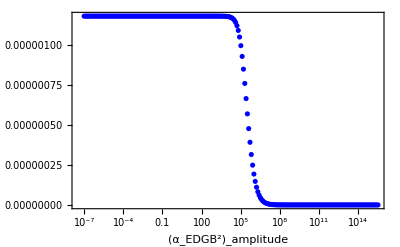

```mathematica
plotαFinalPDFampLogNorm=ListLogLinearPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}]
```

General::munfl: -(1.43419×10^-303)/(6.50391×10^14) is too small to represent as a normalized machine number; precision may be lost.

{{0,0},{1.×10^-7,1.17799×10^-13},{1.25893×10^-7,1.483×10^-13},{1.58489×10^-7,1.86699×10^-13},{1.99526×10^-7,2.3504×10^-13},{2.51189×10^-7,2.95898×10^-13},{3.16228×10^-7,3.72514×10^-13},{3.98107×10^-7,4.68967×10^-13},{5.01187×10^-7,5.90395×10^-13},{6.30957×10^-7,7.43263×10^-13},{7.94328×10^-7,9.35713×10^-13},{1.×10^-6,1.17799×10^-12},{1.25893×10^-6,1.483×10^-12},{1.58489×10^-6,1.86699×10^-12},{1.99526×10^-6,2.3504×10^-12},{2.51189×10^-6,2.95898×10^-12},{3.16228×10^-6,3.72514×10^-12},{3.98107×10^-6,4.68967×10^-12},{5.01187×10^-6,5.90395×10^-12},{6.30957×10^-6,7.43263×10^-12},{7.94328×10^-6,9.35713×10^-12},{0.00001,1.17799×10^-11},{0.0000125893,1.483×10^-11},{0.0000158489,1.86699×10^-11},{0.0000199526,2.3504×10^-11},{0.0000251189,2.95898×10^-11},{0.0000316228,3.72514×10^-11},{0.0000398107,4.68967×10^-11},{0.0000501187,5.90395×10^-11},{0.0000630957,7.43263×10^-11},{0.0000794328,9.35713×10^-11},{0.0001,1.17799×10^-10},{0.000125893,1.483×10^-10},{0.000158489,1.86699×10^-10},{0.000199526,2.3504×10^-10},{0.000251189,2.95898×10^-10},{0.000316228,3.72514×10^-10},{0.000398107,4.68967×10^-10},{0.000501187,5.90395×10^-10},{0.000630957,7.43263×10^-10},{0.000794328,9.35713×10^-10},{0.001,1.17799×10^-9},{0.00125893,1.483×10^-9},{0.00158489,1.86699×10^-9},{0.00199526,2.3504×10^-9},{0.00251189,2.95898×10^-9},{0.00316228,3.72514×10^-9},{0.00398107,4.68967×10^-9},{0.00501187,5.90395×10^-9},{0.00630957,7.43263×10^-9},{0.00794328,9.35713×10^-9},{0.01,1.17799×10^-8},{0.0125893,1.483×10^-8},{0.0158489,1.86699×10^-8},{0.0199526,2.3504×10^-8},{0.0251189,2.95898×10^-8},{0.0316228,3.72514×10^-8},{0.0398107,4.68967×10^-8},{0.0501187,5.90395×10^-8},{0.0630957,7.43263×10^-8},{0.0794328,9.35713×10^-8},{0.1,1.17799×10^-7},{0.125893,1.483×10^-7},{0.158489,1.86699×10^-7},{0.199526,2.3504×10^-7},{0.251189,2.95898×10^-7},{0.316228,3.72514×10^-7},{0.398107,4.68967×10^-7},{0.501187,5.90395×10^-7},{0.630957,7.43263×10^-7},{0.794328,9.35713×10^-7},{1.,1.17799×10^-6},{1.25893,1.483×10^-6},{1.58489,1.86699×10^-6},{1.99526,2.3504×10^-6},{2.51189,2.95898×10^-6},{3.16228,3.72514×10^-6},{3.98107,4.68967×10^-6},{5.01187,5.90395×10^-6},{6.30957,7.43263×10^-6},{7.94328,9.35713×10^-6},{10.,0.0000117799},{12.5893,0.00001483},{15.8489,0.0000186699},{19.9526,0.000023504},{25.1189,0.0000295898},{31.6228,0.0000372514},{39.8107,0.0000468967},{50.1187,0.0000590395},{63.0957,0.0000743263},{79.4328,0.0000935712},{100.,0.000117799},{125.893,0.0001483},{158.489,0.000186699},{199.526,0.00023504},{251.189,0.000295898},{316.228,0.000372514},{398.107,0.000468967},{501.187,0.000590394},{630.957,0.000743261},{794.328,0.000935708},{1000.,0.00117798},{1258.93,0.00148299},{1584.89,0.00186696},{1995.26,0.00235033},{2511.89,0.00295884},{3162.28,0.00372486},{3981.07,0.00468911},{5011.87,0.00590283},{6309.57,0.0074304},{7943.28,0.00935268},{10000.,0.0117711},{12589.3,0.0148124},{15848.9,0.0186348},{19952.6,0.0234343},{25118.9,0.0294517},{31622.8,0.0369785},{39810.7,0.0463609},{50118.7,0.0579959},{63095.7,0.0723187},{79432.8,0.0897732},{100000.,0.110769},{125893.,0.135626},{158489.,0.164516},{199526.,0.19741},{251189.,0.234053},{316228.,0.27398},{398107.,0.316548},{501187.,0.360988},{630957.,0.406448},{794328.,0.452047},{1.×10^6,0.496943},{1.25893×10^6,0.540398},{1.58489×10^6,0.581825},{1.99526×10^6,0.620813},{2.51189×10^6,0.657116},{3.16228×10^6,0.690637},{3.98107×10^6,0.721384},{5.01187×10^6,0.749435},{6.30957×10^6,0.774912},{7.94328×10^6,0.797976},{1.×10^7,0.818822},{1.25893×10^7,0.837654},{1.58489×10^7,0.854669},{1.99526×10^7,0.870041},{2.51189×10^7,0.883922},{3.16228×10^7,0.896438},{3.98107×10^7,0.907688},{5.01187×10^7,0.91776},{6.30957×10^7,0.926743},{7.94328×10^7,0.934745},{1.×10^8,0.941886},{1.25893×10^8,0.948276},{1.58489×10^8,0.954008},{1.99526×10^8,0.959151},{2.51189×10^8,0.963763},{3.16228×10^8,0.967886},{3.98107×10^8,0.971559},{5.01187×10^8,0.974822},{6.30957×10^8,0.97771},{7.94328×10^8,0.980259},{1.×10^9,0.982501},{1.25893×10^9,0.984466},{1.58489×10^9,0.986188},{1.99526×10^9,0.987699},{2.51189×10^9,0.989032},{3.16228×10^9,0.990214},{3.98107×10^9,0.991266},{5.01187×10^9,0.992201},{6.30957×10^9,0.993025},{7.94328×10^9,0.993746},{1.×10^10,0.994373},{1.25893×10^10,0.99492},{1.58489×10^10,0.995403},{1.99526×10^10,0.995838},{2.51189×10^10,0.996238},{3.16228×10^10,0.996611},{3.98107×10^10,0.996964},{5.01187×10^10,0.997296},{6.30957×10^10,0.997606},{7.94328×10^10,0.99789},{1.×10^11,0.998148},{1.25893×10^11,0.998378},{1.58489×10^11,0.998577},{1.99526×10^11,0.998747},{2.51189×10^11,0.998889},{3.16228×10^11,0.999008},{3.98107×10^11,0.999112},{5.01187×10^11,0.999208},{6.30957×10^11,0.999298},{7.94328×10^11,0.999384},{1.×10^12,0.999466},{1.25893×10^12,0.999544},{1.58489×10^12,0.999617},{1.99526×10^12,0.999684},{2.51189×10^12,0.999745},{3.16228×10^12,0.999799},{3.98107×10^12,0.999845},{5.01187×10^12,0.999884},{6.30957×10^12,0.999916},{7.94328×10^12,0.999941},{1.×10^13,0.99996},{1.25893×10^13,0.999974},{1.58489×10^13,0.999983},{1.99526×10^13,0.99999},{2.51189×10^13,0.999995},{3.16228×10^13,0.999998},{3.98107×10^13,0.999999},{5.01187×10^13,1.},{6.30957×10^13,1.},{7.94328×10^13,1.},{1.×10^14,1.},{1.25893×10^14,1.},{1.58489×10^14,1.},{1.99526×10^14,1.},{2.51189×10^14,1.},{3.16228×10^14,1.},{3.98107×10^14,1.},{5.01187×10^14,1.},{6.30957×10^14,1.},{7.94328×10^14,1.},{1.×10^15,1.},{1.25893×10^15,1.},{1.58489×10^15,1.},{1.99526×10^15,1.},{2.51189×10^15,1.},{3.16228×10^15,1.}}

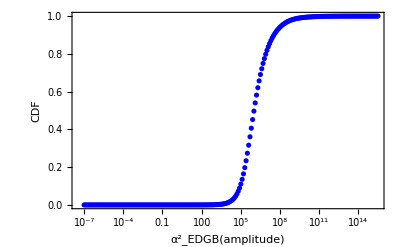

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

3.39033×10^7

```mathematica
√√αSquared90CLamp
```

76.3063

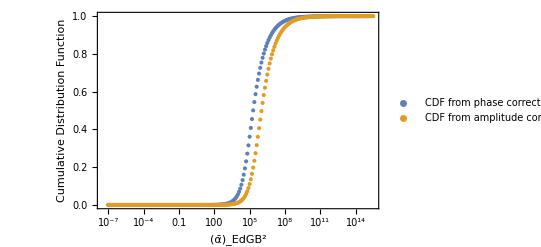

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True] (*Shows that indeed for GW150914, the amplitude and phase corrections are comparable*)
```

Combined Correction

```mathematica
LogSquaredαcomb=Log[SqrtαEDGBcomb^4] (*This is Log of sigma_(alpha^2)*)
```

{13.6127,12.1472,10.9958,20.1656,14.5952,10.3038,14.975,11.628,16316,13.1335,10.9647,11.6417,11.6058,11.7846,10.0174,10.7112,12.2773}
 |  |  |  |

```mathematica
MaxLogSquaredαcomb=Max[LogSquaredαcomb]
```

31.9591

```mathematica
MinLogSquaredαcomb=Min[LogSquaredαcomb]
```

9.08502

```mathematica
𝒟logαcomb=HistogramDistribution[LogSquaredαcomb] ;
```

```mathematica
pslogαcomb=PDF[𝒟logαcomb,x];
```

```mathematica
Histogram[LogSquaredαcomb];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLogcomb=Prepend[10^Range[-7,15.5,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αcombTable[y_]=Table[{αSampleLogcomb[[i]],fun1αphase[αSampleLogcomb[[i]],y]},{i,1,Length[αSampleLogcomb]}];
```

```mathematica
(*αcombMC[x_]=pslogαcomb;*)
```

```mathematica
𝒟logαSqcomb=SmoothKernelDistribution[LogSquaredαcomb]
```

DataDistribution[…]

```mathematica
𝒟logαSqcomb2=PDF[𝒟logαSqcomb,x]
```

Piecewise[{{InterpolatingFunction[…][x], 7.85006≤x≤33.194}, {0, True}}]

```mathematica
𝒟logαSqcomb3[x_]=𝒟logαSqcomb2
```

Piecewise[{{InterpolatingFunction[…][x], 7.85006≤x≤33.194}, {0, True}}]

```mathematica
(*Plot[𝒟logαSqcomb3[x],{x,4,37},PlotRange->All]*)
```

```mathematica
(*αcombMC[8]*)
```

```mathematica
(*αcombMC[32]*)
```

```mathematica
(*αMCSample=Range[7,32,1]*)
```

```mathematica
(*αMCTablecomb=Table[{αMCSample[[i]],αcombMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];*)
```

```mathematica
(*αMCTableInterpcomb=Interpolation[αMCTablecomb];*)
```

```mathematica
(*plotαMCTableInterpcomb=Plot[αMCTableInterpcomb[x],{x,5,37},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]*)
```

```mathematica
(*plot8=Plot[αcombMC[x],{x,5,37},Filling->Axis,PlotStyle->Gray,PlotRange->All]*)
```

```mathematica
(*Show[plot8,plotαMCTableInterpcomb] (*Interpolation matches the actual pdf of monte-carlo*)*)
```

```mathematica
αFinalPDFcombLog=Table[{fun1αcombTable[y][[i,1]],NIntegrate[fun1αcombTable[y][[i,2]]*𝒟logαSqcomb3[y],{y,MinLogSquaredαcomb,MaxLogSquaredαcomb}]},{i,1,Length[fun1αcombTable[y]]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0,2.60366×10^-6},{1.×10^-7,2.60366×10^-6},{1.25893×10^-7,2.60366×10^-6},{1.58489×10^-7,2.60366×10^-6},{1.99526×10^-7,2.60366×10^-6},{2.51189×10^-7,2.60366×10^-6},{3.16228×10^-7,2.60366×10^-6},{3.98107×10^-7,2.60366×10^-6},{5.01187×10^-7,2.60366×10^-6},{6.30957×10^-7,2.60366×10^-6},{7.94328×10^-7,2.60366×10^-6},{1.×10^-6,2.60366×10^-6},{1.25893×10^-6,2.60366×10^-6},{1.58489×10^-6,2.60366×10^-6},{1.99526×10^-6,2.60366×10^-6},{2.51189×10^-6,2.60366×10^-6},{3.16228×10^-6,2.60366×10^-6},{3.98107×10^-6,2.60366×10^-6},{5.01187×10^-6,2.60366×10^-6},{6.30957×10^-6,2.60366×10^-6},{7.94328×10^-6,2.60366×10^-6},{0.00001,2.60366×10^-6},{0.0000125893,2.60366×10^-6},{0.0000158489,2.60366×10^-6},{0.0000199526,2.60366×10^-6},{0.0000251189,2.60366×10^-6},{0.0000316228,2.60366×10^-6},{0.0000398107,2.60366×10^-6},{0.0000501187,2.60366×10^-6},{0.0000630957,2.60366×10^-6},{0.0000794328,2.60366×10^-6},{0.0001,2.60366×10^-6},{0.000125893,2.60366×10^-6},{0.000158489,2.60366×10^-6},{0.000199526,2.60366×10^-6},{0.000251189,2.60366×10^-6},{0.000316228,2.60366×10^-6},{0.000398107,2.60366×10^-6},{0.000501187,2.60366×10^-6},{0.000630957,2.60366×10^-6},{0.000794328,2.60366×10^-6},{0.001,2.60366×10^-6},{0.00125893,2.60366×10^-6},{0.00158489,2.60366×10^-6},{0.00199526,2.60366×10^-6},{0.00251189,2.60366×10^-6},{0.00316228,2.60366×10^-6},{0.00398107,2.60366×10^-6},{0.00501187,2.60366×10^-6},{0.00630957,2.60366×10^-6},{0.00794328,2.60366×10^-6},{0.01,2.60366×10^-6},{0.0125893,2.60366×10^-6},{0.0158489,2.60366×10^-6},{0.0199526,2.60366×10^-6},{0.0251189,2.60366×10^-6},{0.0316228,2.60366×10^-6},{0.0398107,2.60366×10^-6},{0.0501187,2.60366×10^-6},{0.0630957,2.60366×10^-6},{0.0794328,2.60366×10^-6},{0.1,2.60366×10^-6},{0.125893,2.60366×10^-6},{0.158489,2.60366×10^-6},{0.199526,2.60366×10^-6},{0.251189,2.60366×10^-6},{0.316228,2.60366×10^-6},{0.398107,2.60366×10^-6},{0.501187,2.60366×10^-6},{0.630957,2.60366×10^-6},{0.794328,2.60366×10^-6},{1.,2.60366×10^-6},{1.25893,2.60366×10^-6},{1.58489,2.60366×10^-6},{1.99526,2.60366×10^-6},{2.51189,2.60366×10^-6},{3.16228,2.60366×10^-6},{3.98107,2.60366×10^-6},{5.01187,2.60366×10^-6},{6.30957,2.60366×10^-6},{7.94328,2.60366×10^-6},{10.,2.60366×10^-6},{12.5893,2.60366×10^-6},{15.8489,2.60366×10^-6},{19.9526,2.60366×10^-6},{25.1189,2.60366×10^-6},{31.6228,2.60366×10^-6},{39.8107,2.60366×10^-6},{50.1187,2.60366×10^-6},{63.0957,2.60366×10^-6},{79.4328,2.60365×10^-6},{100.,2.60365×10^-6},{125.893,2.60364×10^-6},{158.489,2.60364×10^-6},{199.526,2.60362×10^-6},{251.189,2.6036×10^-6},{316.228,2.60356×10^-6},{398.107,2.6035×10^-6},{501.187,2.60341×10^-6},{630.957,2.60327×10^-6},{794.328,2.60304×10^-6},{1000.,2.60267×10^-6},{1258.93,2.6021×10^-6},{1584.89,2.60118×10^-6},{1995.26,2.59974×10^-6},{2511.89,2.59746×10^-6},{3162.28,2.59386×10^-6},{3981.07,2.58821×10^-6},{5011.87,2.57935×10^-6},{6309.57,2.56558×10^-6},{7943.28,2.5444×10^-6},{10000.,2.51231×10^-6},{12589.3,2.4648×10^-6},{15848.9,2.39664×10^-6},{19952.6,2.30271×10^-6},{25118.9,2.17927×10^-6},{31622.8,2.02513×10^-6},{39810.7,1.8426×10^-6},{50118.7,1.63803×10^-6},{63095.7,1.42132×10^-6},{79432.8,1.20399×10^-6},{100000.,9.96579×10^-7},{125893.,8.06946×10^-7},{158489.,6.39848×10^-7},{199526.,4.97415×10^-7},{251189.,3.79735×10^-7},{316228.,2.85328×10^-7},{398107.,2.1162×10^-7},{501187.,1.55418×10^-7},{630957.,1.1334×10^-7},{794328.,8.22197×10^-8},{1.×10^6,5.9382×10^-8},{1.25893×10^6,4.2731×10^-8},{1.58489×10^6,3.06741×10^-8},{1.99526×10^6,2.19981×10^-8},{2.51189×10^6,1.57759×10^-8},{3.16228×10^6,1.13151×10^-8},{3.98107×10^6,8.11441×10^-9},{5.01187×10^6,5.81503×10^-9},{6.30957×10^6,4.15973×10^-9},{7.94328×10^6,2.96566×10^-9},{1.×10^7,2.10539×10^-9},{1.25893×10^7,1.49002×10^-9},{1.58489×10^7,1.05434×10^-9},{1.99526×10^7,7.47912×10^-10},{2.51189×10^7,5.32146×10^-10},{3.16228×10^7,3.79319×10^-10},{3.98107×10^7,2.70431×10^-10},{5.01187×10^7,1.92493×10^-10},{6.30957×10^7,1.36566×10^-10},{7.94328×10^7,9.6512×10^-11},{1.×10^8,6.79863×10^-11},{1.25893×10^8,4.77594×10^-11},{1.58489×10^8,3.34408×10^-11},{1.99526×10^8,2.33358×10^-11},{2.51189×10^8,1.62485×10^-11},{3.16228×10^8,1.13117×10^-11},{3.98107×10^8,7.89319×10^-12},{5.01187×10^8,5.53438×10^-12},{6.30957×10^8,3.90217×10^-12},{7.94328×10^8,2.75869×10^-12},{1.×10^9,1.94351×10^-12},{1.25893×10^9,1.35705×10^-12},{1.58489×10^9,9.39308×10^-13},{1.99526×10^9,6.48816×10^-13},{2.51189×10^9,4.51424×10^-13},{3.16228×10^9,3.18898×10^-13},{3.98107×10^9,2.29738×10^-13},{5.01187×10^9,1.68737×10^-13},{6.30957×10^9,1.25756×10^-13},{7.94328×10^9,9.42679×10^-14},{1.×10^10,7.0317×10^-14},{1.25893×10^10,5.18033×10^-14},{1.58489×10^10,3.76127×10^-14},{1.99526×10^10,2.69056×10^-14},{2.51189×10^10,1.89136×10^-14},{3.16228×10^10,1.30024×10^-14},{3.98107×10^10,8.72652×10^-15},{5.01187×10^10,5.78572×10^-15},{6.30957×10^10,3.89984×10^-15},{7.94328×10^10,2.74499×10^-15},{1.×10^11,2.01871×10^-15},{1.25893×10^11,1.52063×10^-15},{1.58489×10^11,1.15337×10^-15},{1.99526×10^11,8.74567×10^-16},{2.51189×10^11,6.59629×10^-16},{3.16228×10^11,4.90971×10^-16},{3.98107×10^11,3.57878×10^-16},{5.01187×10^11,2.54547×10^-16},{6.30957×10^11,1.76844×10^-16},{7.94328×10^11,1.20468×10^-16},{1.×10^12,8.06689×10^-17},{1.25893×10^12,5.28794×10^-17},{1.58489×10^12,3.35632×10^-17},{1.99526×10^12,2.04785×10^-17},{2.51189×10^12,1.2163×10^-17},{3.16228×10^12,7.27062×10^-18},{3.98107×10^12,4.47603×10^-18},{5.01187×10^12,2.81839×10^-18},{6.30957×10^12,1.835×10^-18},{7.94328×10^12,1.32296×10^-18},{1.×10^13,1.10473×10^-18},{1.25893×10^13,1.01157×10^-18},{1.58489×10^13,9.40884×10^-19},{1.99526×10^13,8.53027×10^-19},{2.51189×10^13,7.37699×10^-19},{3.16228×10^13,5.97264×10^-19},{3.98107×10^13,4.44873×10^-19},{5.01187×10^13,3.01965×10^-19},{6.30957×10^13,1.88139×10^-19},{7.94328×10^13,1.0957×10^-19},{1.×10^14,5.89905×10^-20},{1.25893×10^14,2.70302×10^-20},{1.58489×10^14,9.08793×10^-21},{1.99526×10^14,1.8352×10^-21},{2.51189×10^14,1.68062×10^-22},{3.16228×10^14,4.54015×10^-24},{3.98107×10^14,1.82864×10^-26},{5.01187×10^14,3.69455×10^-30},{6.30957×10^14,6.60579×10^-36},{7.94328×10^14,6.64185×10^-45},{1.×10^15,4.74111×10^-59},{1.25893×10^15,2.34643×10^-81},{1.58489×10^15,1.36284×10^-116},{1.99526×10^15,2.54412×10^-172},{2.51189×10^15,1.57694×10^-260},{3.16228×10^15,0.}}

```mathematica
αFinalPDFcombInterpLog=Interpolation[αFinalPDFcombLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationcomb=NIntegrate[αFinalPDFcombInterpLog[x],{x,0,3.16227*10^15}]
```

0.499359

```mathematica
αFinalPDFcombLogNorm=Table[{αFinalPDFcombLog[[i,1]],αFinalPDFcombLog[[i,2]]/αNormalizationcomb},{i,1,Length[αFinalPDFcombLog]}]
```

{{0,5.214×10^-6},{1.×10^-7,5.214×10^-6},{1.25893×10^-7,5.214×10^-6},{1.58489×10^-7,5.214×10^-6},{1.99526×10^-7,5.214×10^-6},{2.51189×10^-7,5.214×10^-6},{3.16228×10^-7,5.214×10^-6},{3.98107×10^-7,5.214×10^-6},{5.01187×10^-7,5.214×10^-6},{6.30957×10^-7,5.214×10^-6},{7.94328×10^-7,5.214×10^-6},{1.×10^-6,5.214×10^-6},{1.25893×10^-6,5.214×10^-6},{1.58489×10^-6,5.214×10^-6},{1.99526×10^-6,5.214×10^-6},{2.51189×10^-6,5.214×10^-6},{3.16228×10^-6,5.214×10^-6},{3.98107×10^-6,5.214×10^-6},{5.01187×10^-6,5.214×10^-6},{6.30957×10^-6,5.214×10^-6},{7.94328×10^-6,5.214×10^-6},{0.00001,5.214×10^-6},{0.0000125893,5.214×10^-6},{0.0000158489,5.214×10^-6},{0.0000199526,5.214×10^-6},{0.0000251189,5.214×10^-6},{0.0000316228,5.214×10^-6},{0.0000398107,5.214×10^-6},{0.0000501187,5.214×10^-6},{0.0000630957,5.214×10^-6},{0.0000794328,5.214×10^-6},{0.0001,5.214×10^-6},{0.000125893,5.214×10^-6},{0.000158489,5.214×10^-6},{0.000199526,5.214×10^-6},{0.000251189,5.214×10^-6},{0.000316228,5.214×10^-6},{0.000398107,5.214×10^-6},{0.000501187,5.214×10^-6},{0.000630957,5.214×10^-6},{0.000794328,5.214×10^-6},{0.001,5.214×10^-6},{0.00125893,5.214×10^-6},{0.00158489,5.214×10^-6},{0.00199526,5.214×10^-6},{0.00251189,5.214×10^-6},{0.00316228,5.214×10^-6},{0.00398107,5.214×10^-6},{0.00501187,5.214×10^-6},{0.00630957,5.214×10^-6},{0.00794328,5.214×10^-6},{0.01,5.214×10^-6},{0.0125893,5.214×10^-6},{0.0158489,5.214×10^-6},{0.0199526,5.214×10^-6},{0.0251189,5.214×10^-6},{0.0316228,5.214×10^-6},{0.0398107,5.214×10^-6},{0.0501187,5.214×10^-6},{0.0630957,5.214×10^-6},{0.0794328,5.214×10^-6},{0.1,5.214×10^-6},{0.125893,5.214×10^-6},{0.158489,5.214×10^-6},{0.199526,5.214×10^-6},{0.251189,5.214×10^-6},{0.316228,5.214×10^-6},{0.398107,5.214×10^-6},{0.501187,5.214×10^-6},{0.630957,5.214×10^-6},{0.794328,5.214×10^-6},{1.,5.214×10^-6},{1.25893,5.214×10^-6},{1.58489,5.214×10^-6},{1.99526,5.214×10^-6},{2.51189,5.214×10^-6},{3.16228,5.214×10^-6},{3.98107,5.214×10^-6},{5.01187,5.214×10^-6},{6.30957,5.214×10^-6},{7.94328,5.214×10^-6},{10.,5.214×10^-6},{12.5893,5.214×10^-6},{15.8489,5.214×10^-6},{19.9526,5.214×10^-6},{25.1189,5.214×10^-6},{31.6228,5.214×10^-6},{39.8107,5.214×10^-6},{50.1187,5.214×10^-6},{63.0957,5.214×10^-6},{79.4328,5.21399×10^-6},{100.,5.21398×10^-6},{125.893,5.21397×10^-6},{158.489,5.21395×10^-6},{199.526,5.21392×10^-6},{251.189,5.21388×10^-6},{316.228,5.21381×10^-6},{398.107,5.21369×10^-6},{501.187,5.21351×10^-6},{630.957,5.21322×10^-6},{794.328,5.21276×10^-6},{1000.,5.21203×10^-6},{1258.93,5.21087×10^-6},{1584.89,5.20904×10^-6},{1995.26,5.20615×10^-6},{2511.89,5.20159×10^-6},{3162.28,5.19438×10^-6},{3981.07,5.18306×10^-6},{5011.87,5.16532×10^-6},{6309.57,5.13775×10^-6},{7943.28,5.09532×10^-6},{10000.,5.03107×10^-6},{12589.3,4.93593×10^-6},{15848.9,4.79943×10^-6},{19952.6,4.61133×10^-6},{25118.9,4.36413×10^-6},{31622.8,4.05545×10^-6},{39810.7,3.68992×10^-6},{50118.7,3.28026×10^-6},{63095.7,2.8463×10^-6},{79432.8,2.41107×10^-6},{100000.,1.99572×10^-6},{125893.,1.61596×10^-6},{158489.,1.28134×10^-6},{199526.,9.96106×10^-7},{251189.,7.60444×10^-7},{316228.,5.71388×10^-7},{398107.,4.23784×10^-7},{501187.,3.11234×10^-7},{630957.,2.26971×10^-7},{794328.,1.6465×10^-7},{1.×10^6,1.18916×10^-7},{1.25893×10^6,8.55717×10^-8},{1.58489×10^6,6.1427×10^-8},{1.99526×10^6,4.40526×10^-8},{2.51189×10^6,3.15922×10^-8},{3.16228×10^6,2.26593×10^-8},{3.98107×10^6,1.62496×10^-8},{5.01187×10^6,1.1645×10^-8},{6.30957×10^6,8.33014×10^-9},{7.94328×10^6,5.93893×10^-9},{1.×10^7,4.21619×10^-9},{1.25893×10^7,2.98386×10^-9},{1.58489×10^7,2.11139×10^-9},{1.99526×10^7,1.49774×10^-9},{2.51189×10^7,1.06566×10^-9},{3.16228×10^7,7.59612×10^-10},{3.98107×10^7,5.41557×10^-10},{5.01187×10^7,3.8548×10^-10},{6.30957×10^7,2.73483×10^-10},{7.94328×10^7,1.93272×10^-10},{1.×10^8,1.36147×10^-10},{1.25893×10^8,9.56414×10^-11},{1.58489×10^8,6.69675×10^-11},{1.99526×10^8,4.67315×10^-11},{2.51189×10^8,3.25388×10^-11},{3.16228×10^8,2.26525×10^-11},{3.98107×10^8,1.58066×10^-11},{5.01187×10^8,1.1083×10^-11},{6.30957×10^8,7.81437×10^-12},{7.94328×10^8,5.52446×10^-12},{1.×10^9,3.892×10^-12},{1.25893×10^9,2.71758×10^-12},{1.58489×10^9,1.88103×10^-12},{1.99526×10^9,1.2993×10^-12},{2.51189×10^9,9.04007×10^-13},{3.16228×10^9,6.38614×10^-13},{3.98107×10^9,4.60066×10^-13},{5.01187×10^9,3.37908×10^-13},{6.30957×10^9,2.51834×10^-13},{7.94328×10^9,1.88778×10^-13},{1.×10^10,1.40815×10^-13},{1.25893×10^10,1.0374×10^-13},{1.58489×10^10,7.5322×10^-14},{1.99526×10^10,5.38803×10^-14},{2.51189×10^10,3.78758×10^-14},{3.16228×10^10,2.60381×10^-14},{3.98107×10^10,1.74754×10^-14},{5.01187×10^10,1.15863×10^-14},{6.30957×10^10,7.80969×10^-15},{7.94328×10^10,5.49702×10^-15},{1.×10^11,4.0426×10^-15},{1.25893×10^11,3.04515×10^-15},{1.58489×10^11,2.30969×10^-15},{1.99526×10^11,1.75138×10^-15},{2.51189×10^11,1.32095×10^-15},{3.16228×10^11,9.83202×10^-16},{3.98107×10^11,7.16675×10^-16},{5.01187×10^11,5.09748×10^-16},{6.30957×10^11,3.54142×10^-16},{7.94328×10^11,2.41246×10^-16},{1.×10^12,1.61545×10^-16},{1.25893×10^12,1.05895×10^-16},{1.58489×10^12,6.72126×10^-17},{1.99526×10^12,4.10097×10^-17},{2.51189×10^12,2.43571×10^-17},{3.16228×10^12,1.45599×10^-17},{3.98107×10^12,8.96355×10^-18},{5.01187×10^12,5.64402×10^-18},{6.30957×10^12,3.67471×10^-18},{7.94328×10^12,2.64931×10^-18},{1.×10^13,2.21229×10^-18},{1.25893×10^13,2.02573×10^-18},{1.58489×10^13,1.88418×10^-18},{1.99526×10^13,1.70824×10^-18},{2.51189×10^13,1.47729×10^-18},{3.16228×10^13,1.19606×10^-18},{3.98107×10^13,8.90887×10^-19},{5.01187×10^13,6.04704×10^-19},{6.30957×10^13,3.76762×10^-19},{7.94328×10^13,2.1942×10^-19},{1.×10^14,1.18132×10^-19},{1.25893×10^14,5.41297×10^-20},{1.58489×10^14,1.81992×10^-20},{1.99526×10^14,3.67511×10^-21},{2.51189×10^14,3.36556×10^-22},{3.16228×10^14,9.09196×10^-24},{3.98107×10^14,3.66197×10^-26},{5.01187×10^14,7.39858×10^-30},{6.30957×10^14,1.32285×10^-35},{7.94328×10^14,1.33007×10^-44},{1.×10^15,9.49438×10^-59},{1.25893×10^15,4.69888×10^-81},{1.58489×10^15,2.72917×10^-116},{1.99526×10^15,5.09477×10^-172},{2.51189×10^15,3.15794×10^-260},{3.16228×10^15,0.}}

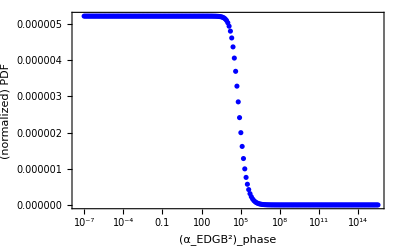

```mathematica
plotαFinalPDFcombLogNorm=ListLogLinearPlot[{αFinalPDFcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFcombInterpLogNorm=Interpolation[αFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFcombNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFcombInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}]
```

{{0,0},{1.×10^-7,5.214×10^-13},{1.25893×10^-7,6.56404×10^-13},{1.58489×10^-7,8.26364×10^-13},{1.99526×10^-7,1.04033×10^-12},{2.51189×10^-7,1.3097×10^-12},{3.16228×10^-7,1.64881×10^-12},{3.98107×10^-7,2.07573×10^-12},{5.01187×10^-7,2.61319×10^-12},{6.30957×10^-7,3.28981×10^-12},{7.94328×10^-7,4.14163×10^-12},{1.×10^-6,5.214×10^-12},{1.25893×10^-6,6.56404×10^-12},{1.58489×10^-6,8.26364×10^-12},{1.99526×10^-6,1.04033×10^-11},{2.51189×10^-6,1.3097×10^-11},{3.16228×10^-6,1.64881×10^-11},{3.98107×10^-6,2.07573×10^-11},{5.01187×10^-6,2.61319×10^-11},{6.30957×10^-6,3.28981×10^-11},{7.94328×10^-6,4.14163×10^-11},{0.00001,5.214×10^-11},{0.0000125893,6.56404×10^-11},{0.0000158489,8.26364×10^-11},{0.0000199526,1.04033×10^-10},{0.0000251189,1.3097×10^-10},{0.0000316228,1.64881×10^-10},{0.0000398107,2.07573×10^-10},{0.0000501187,2.61319×10^-10},{0.0000630957,3.28981×10^-10},{0.0000794328,4.14163×10^-10},{0.0001,5.214×10^-10},{0.000125893,6.56404×10^-10},{0.000158489,8.26364×10^-10},{0.000199526,1.04033×10^-9},{0.000251189,1.3097×10^-9},{0.000316228,1.64881×10^-9},{0.000398107,2.07573×10^-9},{0.000501187,2.61319×10^-9},{0.000630957,3.28981×10^-9},{0.000794328,4.14163×10^-9},{0.001,5.214×10^-9},{0.00125893,6.56404×10^-9},{0.00158489,8.26364×10^-9},{0.00199526,1.04033×10^-8},{0.00251189,1.3097×10^-8},{0.00316228,1.64881×10^-8},{0.00398107,2.07573×10^-8},{0.00501187,2.61319×10^-8},{0.00630957,3.28981×10^-8},{0.00794328,4.14163×10^-8},{0.01,5.214×10^-8},{0.0125893,6.56404×10^-8},{0.0158489,8.26364×10^-8},{0.0199526,1.04033×10^-7},{0.0251189,1.3097×10^-7},{0.0316228,1.64881×10^-7},{0.0398107,2.07573×10^-7},{0.0501187,2.61319×10^-7},{0.0630957,3.28981×10^-7},{0.0794328,4.14163×10^-7},{0.1,5.214×10^-7},{0.125893,6.56404×10^-7},{0.158489,8.26364×10^-7},{0.199526,1.04033×10^-6},{0.251189,1.3097×10^-6},{0.316228,1.64881×10^-6},{0.398107,2.07573×10^-6},{0.501187,2.61319×10^-6},{0.630957,3.28981×10^-6},{0.794328,4.14163×10^-6},{1.,5.214×10^-6},{1.25893,6.56404×10^-6},{1.58489,8.26364×10^-6},{1.99526,0.0000104033},{2.51189,0.000013097},{3.16228,0.0000164881},{3.98107,0.0000207573},{5.01187,0.0000261319},{6.30957,0.0000328981},{7.94328,0.0000414163},{10.,0.00005214},{12.5893,0.0000656404},{15.8489,0.0000826364},{19.9526,0.000104033},{25.1189,0.00013097},{31.6228,0.000164881},{39.8107,0.000207573},{50.1187,0.000261319},{63.0957,0.000328981},{79.4328,0.000414163},{100.,0.0005214},{125.893,0.000656403},{158.489,0.000826361},{199.526,0.00104033},{251.189,0.00130969},{316.228,0.00164879},{398.107,0.00207569},{501.187,0.00261311},{630.957,0.00328965},{794.328,0.0041413},{1000.,0.00521334},{1258.93,0.00656273},{1584.89,0.00826102},{1995.26,0.0103981},{2511.89,0.0130866},{3162.28,0.0164674},{3981.07,0.020716},{5011.87,0.0260499},{6309.57,0.0327357},{7943.28,0.0410957},{10000.,0.0515112},{12589.3,0.0644178},{15848.9,0.0802891},{19952.6,0.0996032},{25118.9,0.12279},{31622.8,0.150166},{39810.7,0.181855},{50118.7,0.21773},{63095.7,0.25739},{79432.8,0.300184},{100000.,0.345283},{125893.,0.39175},{158489.,0.438611},{199526.,0.484916},{251189.,0.52981},{316228.,0.5726},{398107.,0.612797},{501187.,0.650129},{630957.,0.68451},{794328.,0.715985},{1.×10^6,0.744662},{1.25893×10^6,0.770685},{1.58489×10^6,0.794227},{1.99526×10^6,0.815488},{2.51189×10^6,0.834681},{3.16228×10^6,0.85201},{3.98107×10^6,0.867657},{5.01187×10^6,0.881779},{6.30957×10^6,0.89451},{7.94328×10^6,0.905958},{1.×10^7,0.916211},{1.25893×10^7,0.925359},{1.58489×10^7,0.933506},{1.99526×10^7,0.94077},{2.51189×10^7,0.947267},{3.16228×10^7,0.953093},{3.98107×10^7,0.958323},{5.01187×10^7,0.963014},{6.30957×10^7,0.967211},{7.94328×10^7,0.970953},{1.×10^8,0.974276},{1.25893×10^8,0.977219},{1.58489×10^8,0.979817},{1.99526×10^8,0.982104},{2.51189×10^8,0.98411},{3.16228×10^8,0.985868},{3.98107×10^8,0.98741},{5.01187×10^8,0.988768},{6.30957×10^8,0.98997},{7.94328×10^8,0.991038},{1.×10^9,0.991988},{1.25893×10^9,0.992828},{1.58489×10^9,0.993562},{1.99526×10^9,0.994201},{2.51189×10^9,0.994758},{3.16228×10^9,0.995249},{3.98107×10^9,0.99569},{5.01187×10^9,0.996093},{6.30957×10^9,0.99647},{7.94328×10^9,0.996825},{1.×10^10,0.997159},{1.25893×10^10,0.997471},{1.58489×10^10,0.997759},{1.99526×10^10,0.998019},{2.51189×10^10,0.998252},{3.16228×10^10,0.998456},{3.98107×10^10,0.998631},{5.01187×10^10,0.998777},{6.30957×10^10,0.998899},{7.94328×10^10,0.999005},{1.×10^11,0.999101},{1.25893×10^11,0.999192},{1.58489×10^11,0.999278},{1.99526×10^11,0.99936},{2.51189×10^11,0.999438},{3.16228×10^11,0.999512},{3.98107×10^11,0.999581},{5.01187×10^11,0.999643},{6.30957×10^11,0.999698},{7.94328×10^11,0.999746},{1.×10^12,0.999786},{1.25893×10^12,0.99982},{1.58489×10^12,0.999848},{1.99526×10^12,0.999869},{2.51189×10^12,0.999885},{3.16228×10^12,0.999898},{3.98107×10^12,0.999907},{5.01187×10^12,0.999914},{6.30957×10^12,0.99992},{7.94328×10^12,0.999925},{1.×10^13,0.99993},{1.25893×10^13,0.999935},{1.58489×10^13,0.999942},{1.99526×10^13,0.999949},{2.51189×10^13,0.999957},{3.16228×10^13,0.999966},{3.98107×10^13,0.999974},{5.01187×10^13,0.999982},{6.30957×10^13,0.999988},{7.94328×10^13,0.999993},{1.×10^14,0.999996},{1.25893×10^14,0.999999},{1.58489×10^14,1.},{1.99526×10^14,1.},{2.51189×10^14,1.},{3.16228×10^14,1.},{3.98107×10^14,1.},{5.01187×10^14,1.},{6.30957×10^14,1.},{7.94328×10^14,1.},{1.×10^15,1.}}

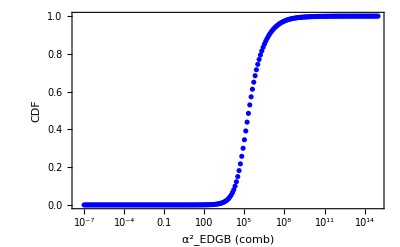

```mathematica
ListLogLinearPlot[αFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (comb)","CDF"}]
```

```mathematica
αFinalCDFcombNormInterp=Interpolation[αFinalCDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
αSquared90CLcomb=x/.FindRoot[αFinalCDFcombNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

7.01894×10^6

```mathematica
√√αSquared90CLcomb//N
```

51.4716

## Small Coupling Approximation

```mathematica
ζphaseAll2=ζphaseAll*1.64485 (*multiplying with 1.64485 since I want to know how much of the data satisfy small coupling with 90% CL*)
```

{0.748761,0.163456,0.0531362,438.938,2.13954,0.0203166,2.21675,16318,0.0535842,0.0896465,0.0995473,0.110349,0.0180631,0.0334412,0.158835}
 |  |  |  |

```mathematica
Max[ζphaseAll2]
```

6.60655×10^7

```mathematica
ζampAll2=ζampAll*1.64485
```

{3.887,0.857518,0.254767,2316.08,11.0546,0.085361,11.8265,0.540324,16316,1.78754,0.258649,0.439418,0.487556,0.544775,0.0815459,0.149686,0.796353}
 |  |  |  |

```mathematica
ζcomball2=ζcombAll*1.64485
```

{0.81043,0.177527,0.057485,476.307,2.3172,0.0218623,2.40842,0.120596,16316,0.402289,0.0579374,0.0971583,0.107759,0.119352,0.0195016,0.0361863,0.172375}
 |  |  |  |

Phase:

```mathematica
𝒟logζphase=HistogramDistribution[Log[ζphaseAll2]]
```

DataDistribution[…]

```mathematica
ps1=PDF[𝒟logζphase,x];
```

```mathematica
ps2[x]=ps1;
```

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll2]],Log[Max[ζphaseAll2]]}]
```

0.999475

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll2]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll2]],Log[Max[ζphaseAll2]]}]*100 (*71% area under the curve satisfies zeta<1 from phase correction*)
```

71.5991

```mathematica
Amplitude
```

```mathematica
𝒟logζamp=HistogramDistribution[Log[ζampAll2]]
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logζamp,x];
```

```mathematica
ps2amp[x]=ps1amp;
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll2]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll2]],Log[Max[ζampAll2]]}]*100
```

41.4272

```mathematica
Combined
```

```mathematica
𝒟logζcomb=HistogramDistribution[Log[ζcomball2]]
```

DataDistribution[…]

```mathematica
ps1comb=PDF[𝒟logζcomb,x];
```

```mathematica
ps2comb[x]=ps1comb;
```

```mathematica
Integrate[ps2comb[x],{x,Log[Min[ζcomball2]],0}]/Integrate[ps2comb[x],{x,Log[Min[ζcomball2]],Log[Max[ζcomball2]]}]*100
```

70.5091

## Exporting data for xmgrace

```mathematica
Export[NotebookDirectory[]<>"cdfphase.dat",αFinalCDFPhaseNorm]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/cdfphase.dat

```mathematica
Export[NotebookDirectory[]<>"cdfamp.dat",αFinalCDFampNorm]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/cdfamp.dat

```mathematica
Export[NotebookDirectory[]<>"cdfcomb.dat",αFinalCDFcombNorm]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/cdfcomb.dat

```mathematica
{bins,counts}=HistogramList[Log[ζphaseAll2],{0.5}]
```

{{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5},{11,103,485,1098,1550,2000,2016,1744,1504,1184,975,758,625,537,360,304,253,178,161,114,86,55,59,37,26,20,16,15,9,14,9,7,2,2,4,4,1,3,0,1,0,0,0,1,0,0,1}}

```mathematica
Table[Append[{bins[[i]]},counts[[i]]],{i,1,Length[counts]}]
```

{{-5.,11},{-4.5,103},{-4.,485},{-3.5,1098},{-3.,1550},{-2.5,2000},{-2.,2016},{-1.5,1744},{-1.,1504},{-0.5,1184},{0.,975},{0.5,758},{1.,625},{1.5,537},{2.,360},{2.5,304},{3.,253},{3.5,178},{4.,161},{4.5,114},{5.,86},{5.5,55},{6.,59},{6.5,37},{7.,26},{7.5,20},{8.,16},{8.5,15},{9.,9},{9.5,14},{10.,9},{10.5,7},{11.,2},{11.5,2},{12.,4},{12.5,4},{13.,1},{13.5,3},{14.,0},{14.5,1},{15.,0},{15.5,0},{16.,0},{16.5,1},{17.,0},{17.5,0},{18.,1}}

```mathematica
{binsamp,countsamp}=HistogramList[Log[ζampAll2],{0.5}]
```

{{-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.},{1,14,114,446,963,1403,1864,1964,1774,1550,1263,1051,809,671,565,402,311,254,219,158,129,100,65,57,41,28,21,16,18,10,13,11,4,4,3,4,3,2,4,0,1,0,0,0,0,1,0,1}}

```mathematica
Table[Append[{binsamp[[i]]},countsamp[[i]]],{i,1,Length[countsamp]}]
```

{{-4.,1},{-3.5,14},{-3.,114},{-2.5,446},{-2.,963},{-1.5,1403},{-1.,1864},{-0.5,1964},{0.,1774},{0.5,1550},{1.,1263},{1.5,1051},{2.,809},{2.5,671},{3.,565},{3.5,402},{4.,311},{4.5,254},{5.,219},{5.5,158},{6.,129},{6.5,100},{7.,65},{7.5,57},{8.,41},{8.5,28},{9.,21},{9.5,16},{10.,18},{10.5,10},{11.,13},{11.5,11},{12.,4},{12.5,4},{13.,3},{13.5,4},{14.,3},{14.5,2},{15.,4},{15.5,0},{16.,1},{16.5,0},{17.,0},{17.5,0},{18.,0},{18.5,1},{19.,0},{19.5,1}}

```mathematica
{binscomb,countscomb}=HistogramList[Log[ζcomball2],{0.5}]
```

{{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5},{7,78,398,999,1496,1928,2065,1778,1529,1240,1014,792,635,551,390,311,246,203,168,114,95,61,56,37,31,19,14,19,7,16,9,4,4,2,4,4,1,4,0,1,0,0,0,0,1,0,1}}

```mathematica
Table[Append[{binscomb[[i]]},countscomb[[i]]],{i,1,Length[countscomb]}]
```

{{-5.,7},{-4.5,78},{-4.,398},{-3.5,999},{-3.,1496},{-2.5,1928},{-2.,2065},{-1.5,1778},{-1.,1529},{-0.5,1240},{0.,1014},{0.5,792},{1.,635},{1.5,551},{2.,390},{2.5,311},{3.,246},{3.5,203},{4.,168},{4.5,114},{5.,95},{5.5,61},{6.,56},{6.5,37},{7.,31},{7.5,19},{8.,14},{8.5,19},{9.,7},{9.5,16},{10.,9},{10.5,4},{11.,4},{11.5,2},{12.,4},{12.5,4},{13.,1},{13.5,4},{14.,0},{14.5,1},{15.,0},{15.5,0},{16.,0},{16.5,0},{17.,1},{17.5,0},{18.,1}}

```mathematica
Export[NotebookDirectory[]<>"zetaphase.dat",Table[Append[{bins[[i]]},counts[[i]]],{i,1,Length[counts]}]]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/zetaphase.dat

```mathematica
Export[NotebookDirectory[]<>"zetaamp.dat",Table[Append[{binsamp[[i]]},countsamp[[i]]],{i,1,Length[countsamp]}]]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/zetaamp.dat

```mathematica
Export[NotebookDirectory[]<>"zetacomb.dat",Table[Append[{binscomb[[i]]},countscomb[[i]]],{i,1,Length[countscomb]}]]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/zetacomb.dat